# Solid quantization for nonpoint particles

[1] P.Wang, Solid quantization for nonpoint particles, Canadian Journal of Physics, 92 (2013) 25 - 30.

## 1. Introduction

The traditional commutation relations are :

we propose new quantization conditions:

```mathematica
Assuming[t∈Reals,
Limit[Integrate[1/(2π I)Exp[I τ t]/(τ-I ϵ),{τ,-Infinity,Infinity}],ϵ->0,Direction->"FromAbove"]
]
```

1/2 (1+Sign[t])

```mathematica
Plot[Evaluate@{Labeled[1/2 (1+Sign[t]),"ans"],Labeled[HeavisideTheta[t],"Theta"]},{t,-3,3}]
```

-Graphics-

## path integral

the gaugeinvariant interaction between the fermion and gauge fields

say a photon field, can be written as

Ld[x](*Lagrangian density*)=∫ⅆ^3 a ψ̄[t,x+a/2]Exp[I*Ii[x+a/2,x]] γμ I Dμ Exp[-I*Ii[x-a/2,x]]ψ[t,x-a/2]F[a]

Dμ=∂μ-I g∫ⅆ^3 b A_μ[t,x+b]G[a,b]

Ii[x,y]=g∫_x^y ⅆzμ∫ⅆ^3 b Aμ[z0,z+b]G[a,b]

G[a,b]=(Φ[a]Φg[b])/F[a]

F[a], fermion size, G[a, b] gauge fields size, Φ[a] correlation between fermions of distance a,
Φg[b]  correlation for gauge fields of distance b,

∫ⅆ^3 a A ψ̄[t,x+a/2]Exp[…] γμ I(∂μ-I g∫ⅆ^3 b A_μ[t,x+b]G[a,b]) Exp[…]ψ[t,x-a/2]F[a]
=∫ⅆ^3 a∫ⅆ^3 b A ψ̄[t,x+a/2] γμ  g∫ⅆ^3 b A_μ[t,x+b](Φ[a]Φg[b])/F[a] ψ[t,x-a/2]F[a]
=∫ⅆ^3 a∫ⅆ^3 b A ψ̄[t,x+a/2] γμ  g∫ⅆ^3 b A_μ[t,x+b]Φ[a]Φg[b] ψ[t,x-a/2]

Dμ[t,x,a]=∂μ-I geff∫ⅆ^3 b A_μ[t,x+b]G[a,b]
ψ[t,x-a/2]→Exp[I geff θ[t,x-a/2]]ψ[t,x-a/2]
ψ̄[t,x+a/2]→Exp[-I geff θ[t,x+a/2]]ψ̄[t,x+a/2]
A_μ[t,x+b]→A_μ[t,x+b]+∂μ θ'[t,x+b]

geff=(Φ[a]Φg[b])/F[a]

Ii[x,y]=g∫_x^y ⅆzμ∫ⅆ^3 b Aμ[z0,z+b]G[a,b]

∫ⅆ^3 b A_μ[t,x+b]G[a,b]→∫ⅆ^3 b A_μ[t,x+b]G[a,b]+∂μ geff θ[t,x+b]
∫ⅆ^3 b A_μ[t,x+b]→∫ⅆ^3 b A_μ[t,x+b]+∂μ ∫ⅆ^3 b θ'[t,x+b]

## finite form

Contrast with the traditional,under a gauge transformation in the follow  (finite form)

Dμ[x]=∂μ[x]-I g A_μ[x]

ψ[x]→ψ[x]Exp[iα[x]Q]
ψ̄[x]→ψ̄[x]Exp[-iα[x]Q]
A_μ[x]→A_μ[x]+1/e∂_μ α[x]
Gauge link transforms as
Exp[-ieQ∫_x^y A^ν[z]ⅆ z^ν]=Exp[iα[x]Q]Exp[-ieQ∫_x^y A^ν[z]ⅆ z^ν]Exp[-iα[y]Q]

Ld0[x]=∫ⅆ^3 a ψ̄[t,x+(a⃗)/2]γμ I ∂μ ψ[t,x-(a⃗)/2]F[a]

→Ld0[x]=∫ⅆ^3 a ψ̄[t,x]γμ I ∂μ ψ[t,x-a⃗]F[a]

→Ld0[x]=∫ⅆ^3 a ψ̄[t,x]γμ I ∂μ( ψ[t,x]+(-a⃗)OverVector[∂]  ψ[t,x]+1/(2!)(-a⃗)^2(OverVector[∂])^2 ψ[t,x]+…)F[a]

→Ld0[x]=∫ⅆ^3 a ψ̄[t,x]γμ I ∂μ( 1+(-a⃗)OverVector[∂] +1/(2!)(-a)^2(OverVector[∂])^2 +…)ψ[t,x]F[a]

→Ld0[x]= ψ̄[t,x]γμ I ∂μ ∫ⅆ^3 a Exp[-a⃗.OverVector[∂]]_(i.e.Exp[Ia⃗.I OverVector[∂]])F[a]ψ[t,x]

→Ld0[x]= ψ̄[t,x]γμ I ∂μ F̃[i∂]ψ[t,x]

The interaction term is written as

Ld0[x]=∫ⅆ^3 a ψ̄[t,x+(a⃗)/2]γμ I ∂μ ψ[t,x-(a⃗)/2]F[a]

Dμ=∂μ-I g∫ⅆ^3 b A_μ[t,x+b]G[a,b]

Ld[x]=∫ⅆ^3 a ψ̄[t,x+a/2]Exp[I*Ii[x+a/2,x]] γμ I Dμ Exp[-I*Ii[x-a/2,x]]ψ[t,x-a/2]F[a]

Ld[x]=∫ⅆ^3 a ψ̄[t,x+a/2]Exp[I*Ii[x+a/2,x]] γμ I (∂μ-I g∫ⅆ^3 b A_μ[t,x+b]G[a,b]) Exp[-I*Ii[x-a/2,x]]ψ[t,x-a/2]F[a]

Ldint[x]=∫ⅆ^3 a ψ̄[t,x+a/2](Exp[I*Ii[x+a/2,x]]) γμ I (∂μ-I g∫ⅆ^3 b A_μ[t,x+b]G[a,b]) (Exp[-I*Ii[x-a/2,x]])ψ[t,x-a/2]F[a]-∫ⅆ^3 a ψ̄[t,x+(a⃗)/2]γμ I ∂μ ψ[t,x-(a⃗)/2]F[a]
=∫ⅆ^3 a ψ̄[t,x+a/2](Exp[I*Ii[x+a/2,x]]-1) γμ I (∂μ) (Exp[-I*Ii[x-a/2,x]])ψ[t,x-a/2]F[a]+
∫ⅆ^3 a ψ̄[t,x+a/2](Exp[I*Ii[x+a/2,x]]) γμ I (∂μ) (Exp[-I*Ii[x-a/2,x]]-1)ψ[t,x-a/2]F[a]+
∫ⅆ^3 a ψ̄[t,x+a/2](Exp[I*Ii[x+a/2,x]]-1) γμ I (∂μ) (Exp[-I*Ii[x-a/2,x]]-1)ψ[t,x-a/2]F[a]+
∫ⅆ^3 a ψ̄[t,x+a/2](Exp[I*Ii[x+a/2,x]]) γμ I (I g∫ⅆ^3 b A_μ[t,x+b]G[a,b]) (Exp[-I*Ii[x-a/2,x]])ψ[t,x-a/2]F[a]

ⅇ^(-ω^2/2)

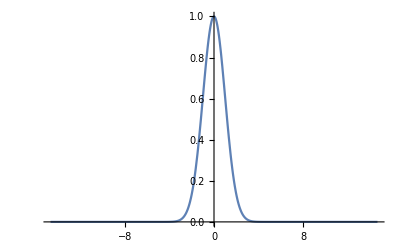

```mathematica
FourierTransform[Exp[-t^2/2],t,ω]
Plot[ⅇ^(-ω^2/2),{ω,-14.696938456699069,14.696938456699069},PlotRange->All]
```

relativistic version of the solid quantization